# Toy Model - 4D

Parameter definition:

```mathematica
Clear["Global`*"]
Ω ={
  {-s, α, 0, 0},
  {0, 0, 0, 0},
  {0, 0, 0, 0},
  {0, 0, 0, 0}
};
Slack = {
{0,0,η,β},
{0,0,-β,η},
{1,0,0,0},
{0,1,0,0}
};
```

```mathematica
Clear["Global`*"]
Ω ={
  {0, 0, 0, 0},
  {-1, 0, 0, 0},
  {0, 0, 0, 0},
  {0, 0, 0, 0}
};
Slack = {
{0,0,ηn,β},
{0,γ,-β,η},
{1,0,0,0},
{0,1,0,0}
};
```

```mathematica
ClearAll[eqns,sol]
(*Define matrix of RHS A*)
(*Considering ω14 = 0 leads to a really expensive calculation of the matrix exponential*)
LinApp = Slack+(Ω/ε);
Print["Resulting linear application :", LinApp //MatrixForm] 
Print["Eigenvalues linear application :", FullSimplify[Eigenvalues[LinApp]]] 
vars = {ϕ[t], ψ[t], A[t], B[t]};
initCond={ϕ[0] == ϕ0, ψ[0] == ψ0, A[0] == A0, B[0] == B0};
(* Construct ODE system *)
full = (LinApp.vars);
eqns = Join[
  Thread[D[vars, t] == full],
  initCond
];
Print["Full system field :", eqns //MatrixForm]
(* Find rows with 1/ε dependece*)
fastRows = Select[Range[Length[full]], ! FreeQ[full[[#]], 1/ε] &];
slowRows = Select[Range[Length[full]], FreeQ[full[[#]], 1/ε] &];
(*Extract these fast equations equations *)
fastEqs = full[[fastRows]];
fastVars = vars[[fastRows]];
slowEqs = Delete[full, List /@ fastRows];
slowVars = vars[[slowRows]];
(* Remove initial conditions for fast variables *)
reducedICs = Select[initCond, FreeQ[#, Alternatives @@ fastVars[[All, 0]]] &];
(*Take ε -> 0 limit to get algebraic constraint *)
algebraicEqs = FullSimplify[Map[# * ε &, fastEqs]];
algebraicEqs = algebraicEqs /. ε -> 0;
algebraicEqs;
(*Solve each fast equation for its associated fast variable *)
criticalManifold = 
  DeleteMissing[
    Table[
      Module[{eq = algebraicEqs[[i]], candidates, sol},
        candidates = Select[vars, ! FreeQ[eq, #] &];
        If[candidates === {}, 
          Missing["NoFastVariableFound"], 
          sol = Quiet@Solve[eq == 0, candidates[[1]]];
          If[sol === {} || ! MatchQ[sol[[1]], _Rule | {__Rule}], 
            Missing["SolveFailed"], 
            sol[[1]]
          ]
        ]
      ],
      {i, Length[algebraicEqs]}
    ]
] //Flatten // FullSimplify;
Print["Number of algebraic constraints: ", Length[fastRows] ]
Print["Critical manifold expression:", criticalManifold //MatrixForm ]
(*Normal hyperbolicity of the critical manifold*)
FastJacobian = D[algebraicEqs,{fastVars}];
```

Resulting linear application :(-s/ε | α/ε | η | β
0 | 0 | -β | η
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Eigenvalues linear application :{Root[β^2 ε^4+ε^4 η^2+(α β ε^2-s ε^2 η) #1-2 ε^2 η #1^2+s #1^3+#1^4&,1]/ε,Root[β^2 ε^4+ε^4 η^2+(α β ε^2-s ε^2 η) #1-2 ε^2 η #1^2+s #1^3+#1^4&,2]/ε,Root[β^2 ε^4+ε^4 η^2+(α β ε^2-s ε^2 η) #1-2 ε^2 η #1^2+s #1^3+#1^4&,3]/ε,Root[β^2 ε^4+ε^4 η^2+(α β ε^2-s ε^2 η) #1-2 ε^2 η #1^2+s #1^3+#1^4&,4]/ε}

Full system field :(ϕ'[t]==η A[t]+β B[t]-(s ϕ[t])/ε+(α ψ[t])/ε
ψ'[t]==-β A[t]+η B[t]
A'[t]==ϕ[t]
B'[t]==ψ[t]
ϕ[0]==ϕ0
ψ[0]==ψ0
A[0]==A0
B[0]==B0)

Number of algebraic constraints: 1

Critical manifold expression:(ϕ[t]→(α ψ[t])/s)

```mathematica
Print["Eigenvalues for normal hyperbolicity:", Eigenvalues[FastJacobian] ]
(*Reduced system with critical manifold*)
reducedSystem = Join[
  Thread[D[slowVars, t] == slowEqs],
  reducedICs
] /. criticalManifold;
Print["Slow vector field :", reducedSystem//MatrixForm]
```

Eigenvalues for normal hyperbolicity:{-s}

Slow vector field :(ψ'[t]==-β A[t]+η B[t]
A'[t]==0
B'[t]==ψ[t]
ψ[0]==ψ0
A[0]==A0
B[0]==B0)

```mathematica
NumRep = {
s -> 0.08,
δ -> 0.01,
α -> 0.1,
β -> 0.1,
η -> 0.1,
ε -> 0.1,
γ -> 0.1,
(*The ω11 the key parameter, as it explodes the linear solution as observed in the full numerical resolution in MatLab*)
p -> 0.1,
ω21 -> 0.1,
(*Values from nonstable equilibrium at b=0.1*)
ϕ0 -> 0.1,
ψ0 -> 0.1,
A0 -> 0.31,
B0 -> 2.48
};
```

```mathematica
Print["Eigenvalues of the fullsystem at nontrivial equilibria: ",Eigenvalues[LinApp] /. NumRep]
(*Numerical matrix exponential of the full system*)
sol = DSolve[eqns, vars, t];
Eigenvalues[LinApp] /. NumRep;
ϕsol[t_] = ϕ[t] /. sol[[1]] /. NumRep;
ψsol[t_] = ψ[t] /. sol[[1]] /. NumRep;
Asol[t_] = A[t] /. sol[[1]] /. NumRep;
Bsol[t_] = B[t] /. sol[[1]] /. NumRep;
(*Numerical matrix exponential of the slow flow*)
solutionSlow = DSolve[reducedSystem, slowVars, t];
slowFunctions = Table[
  Module[{baseSymbol = Head[slowVar], newSym},
    newSym = Symbol[SymbolName[baseSymbol] <> "Slow"];
    newSym[t_] = slowVar /. solutionSlow[[1]] /. NumRep;
    newSym  (* RETURN THE SYMBOL, NOT THE ASSIGNMENT RESULT *)
  ],
  {slowVar, slowVars}
];
```

Eigenvalues of the fullsystem at nontrivial equilibria: {-0.895744,-0.372258,0.234001-0.0722706 ⅈ,0.234001+0.0722706 ⅈ}

For numerical evaluation, we now define the parameters and initial solutions of the system, to understand how it develops. According to the simulations previously performed in MatLab,
α = -0.2, ϵ=0.1, ω12=0, ω=1, X0=0,Y0=0 (because these are the derivatives)

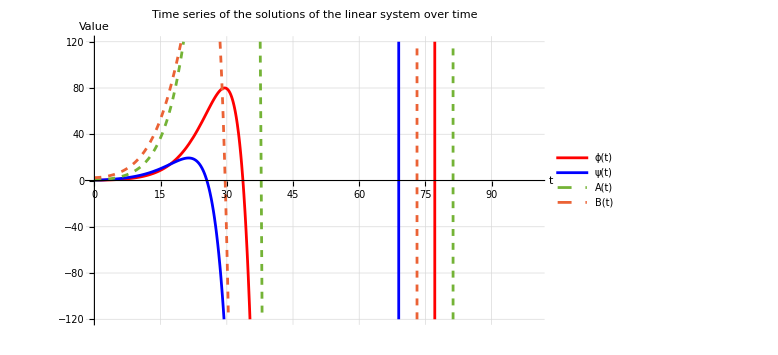

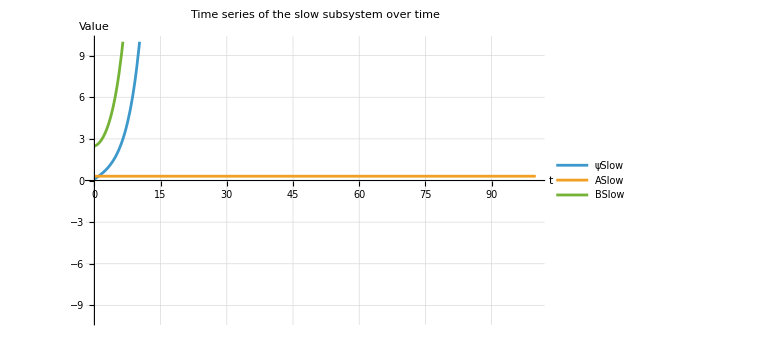

```mathematica
Plot[
  {ϕsol[t], ψsol[t], Asol[t], Bsol[t]},
  {t, 0, 100},
  PlotLegends -> {"ϕ(t)", "ψ(t)", "A(t)", "B(t)"},
  PlotStyle -> {Red, Blue, Dashed, Dashed},
  PlotRange -> {-120,120},
  AxesLabel -> {"t", "Value"},
  GridLines -> Automatic,
  ImageSize -> Large,
  PlotLabel -> "Time series of the solutions of the linear system over time"
]
(*Plot slot dynamics*)
Plot[
  Evaluate[Through[slowFunctions[t]]], 
  {t, 0, 100},
  PlotLegends -> slowFunctions, 
  PlotRange -> {-10,10},
  AxesLabel -> {"t", "Value"},
  GridLines -> Automatic,
  ImageSize -> Large,
  PlotLabel -> "Time series of the slow subsystem over time"
]
```